# Unit 9 - Area approximation, Riemann Sum, and Definite Integral

Topics covered in Unit 9 are listed below.

Area approximation

Riemann sum and definite integral

Finding exact area using Riemann sum

Fundamental theorem of calculus

Evaluating improper integrals

Finding area for complicated cases

Simpson’s 1/3 and 3/8 methods

## Area approximation

Given that a continuous function f(x)≥0 for a≤x≤b, how to approximate the area of the region bounded by x=a,x=b,y=0, and y=f(x)? Usually, we divide the interval [a,b] evenly into n subintervals, where n is a positive integer, and use the sum of the areas of n rectangles (or trapezoids). There are four basic approximations. They are left-endpoint, right-endpoint, midpoint, and trapezoidal approximations.

Usage: PlotShadeInterval[f, a, b, xMin, xMax, abYPos, fYPos, plotRange, ticks, axesLabel]
                        f: the function to  be plotted, f(x)≥0 on [a,b]
                        a: as in [a, b]
                         b: as in [a, b]
                 xMin: as in Plot[f[x],{x,xMin,xMax}], xMin ≤ a
                  xMax: as in Plot[f[x],{x,xMin,xMax}], xMax ≥ b
             abYPos: y-coordinate of the labels a and b on the graph
                fYPos: y-coordinate of the label f(x) on the graph
      plotRange: it must be in the form PlotRange→{y_min,y_max}
                ticks: it must be in the form Ticks→⋯
      axesLabel: it must be in the form AxesLabel→⋯

```mathematica
PlotShadeInterval[func_,a_,b_,xMin_,xMax_,abYPos_,fYPos_,plotRange_,ticks_,axesLabel_]:=
Module[{f},
f[X_]=func/.x->X;
Show[{
Plot[f[x],{x,xMin,xMax},plotRange,ticks,axesLabel,ImageSize->220],
Plot[{f[x],0},{x,a,b},Filling->{1->{2}}],
Graphics[{Text[a,{a,abYPos}]}],
Graphics[{Text[b,{b,abYPos}]}],
Graphics[{Text[f[x],{(xMin+xMax)/2,fYPos}]}]
}]];
```

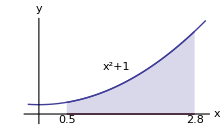

```mathematica
Clear[x]
PlotShadeInterval[x^2+1,0.5,2.8,-0.2,3,-0.6,5,PlotRange->{-0.8,10},Ticks->False,AxesLabel->{x,y}]
```

Figure 1

(1) The left-endpoint approximation uses the value of f(x) at the left-endpoint of a subinterval as the height of the rectangle on the subinterval, as shown in figure 2.

Usage:
PlotLeftEndpointApproximation[f,a,b,n,xMin,xMax,abYPos,fYPos,plotRange,ticks, axesLabel,showExtraMsg]
                             f: the function to be plotted, f(x)≥0 on [a,b]
                             a: as in [a, b]
                             b: as in [a, b]
                             n: the number of subintervals
                     xMin: as in Plot[f[x],{x,xMin,xMax}], xMin ≤ a
                     xMax: as in Plot[f[x],{x,xMin,xMax}], xMax ≥ b
                abYPos: y-coordinate of the labels a and b on the graph
                   fYPos: y-coordinate of the label f(x) on the graph
        plotRange: it must be in the form PlotRange→{y_min,y_max}
                   ticks: it must be in the form Ticks→⋯
         axesLabel: it must be in the form AxesLabel→⋯
 showExtraMsg: print extra message on the graph (see example). Put {} if no extra message.

```mathematica
PlotLeftEndpointApproximation[func_,a_,b_,n_,xMin_,xMax_,abYPos_,fYPos_,plotRange_,ticks_, axesLabel_,showExtraMsg_]:=Module[
{f,h=(b-a)/n},
f[X_]=func/.x->X;
Show[{ 
Plot[f[x],{x,xMin,xMax},plotRange,ticks,axesLabel,ImageSize->250],
Plot[{f[x],0},{x,a,b},Filling->{1->{2}}],
Graphics[{Text[a,{a,abYPos}]}],
Graphics[{Text[b,{b,abYPos}]}],
Graphics[{Text[f[x],{(xMin+xMax)/2,fYPos}]}],
{showExtraMsg},
Graphics[Line[{{a,0},{a,f[a]}}]],
Table[Graphics[Line[{{a+i*h,0},{a+i*h,Max[{f[a+(i-1)h],f[a+i*h]}]}}]],{i,1,n-1}],
Graphics[Line[{{b,0},{b,f[b-h]}}]],
Table[Graphics[Line[{{a+i*h,f[a+i*h]},{a+(i+1)*h,f[a+i*h]}}]],{i,0,n-1}]
}]
]
```

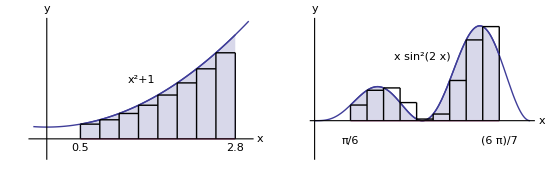

```mathematica
GraphicsRow[{
PlotLeftEndpointApproximation[x^2+1,0.5,2.8,8,-0.2,3,-0.8,5,PlotRange->{-1.5,10},Ticks->False,AxesLabel->{x,y},{}],
PlotLeftEndpointApproximation[x Sin[2x]^2,π/6,6/7 π,9,0,π,-0.5,1.6,PlotRange->{-0.9,2.5},Ticks->False,AxesLabel->{x,y},{}]
}]
```

Figure 2

Let h=△x=(b-a)/n. The true area of the shaded region in Figure 1 is approximated by

∑_(i=1)^n f(a+(i-1)h) h or ∑_(i=0)^(n-1) f(a+i h) h.

```mathematica
LeftEndpointApproximation[func_,a_,b_,n_]:=Module[
{f,h},
f[X_]=func/.x->X;
h=(b-a)/n//N;
Sum[f[a+i h],{i,0,n-1}]*h
];
```

```mathematica
LeftEndpointApproximation[Sin[x],0,Pi,10]
```

1.98352

The animation below helps you explore the approximations using various number of subintervals for sin x over [0,π]. The exact area of the shaded region is 2.

```mathematica
Manipulate[
Module[{f,a,b,toString,PlotLeftEndpointApproximation,LeftEndpointApproximation},
f[x_]:=Sin[x];
a=0;b=π;
toString[x_]:=ToString[If[Abs[x]<10^-5,0,x]];

(* Why copy the two functions below? It is to make the animation always work, and to overcome the constraint of Mathematica on Animate and Manipulate as well. *)
PlotLeftEndpointApproximation[func_,a_,b_,n_,xMin_,xMax_,abYPos_,fYPos_,plotRange_,ticks_, axesLabel_,showExtraMsg_]:=Module[
{f,h=(b-a)/n},
f[X_]=func/.x->X;
Show[{ 
Plot[f[x],{x,xMin,xMax},plotRange,ticks,axesLabel,ImageSize->320],
Plot[{f[x],0},{x,a,b},Filling->{1->{2}}],
Graphics[{Text[a,{a,abYPos}]}],
Graphics[{Text[b,{b,abYPos}]}],
Graphics[{Text[f[x],{(xMin+xMax)/2,fYPos}]}],
{showExtraMsg},
Graphics[Line[{{a,0},{a,f[a]}}]],
Table[Graphics[Line[{{a+i*h,0},{a+i*h,Max[{f[a+(i-1)h],f[a+i*h]}]}}]],{i,1,n-1}],
Graphics[Line[{{b,0},{b,f[b-h]}}]],
Table[Graphics[Line[{{a+i*h,f[a+i*h]},{a+(i+1)*h,f[a+i*h]}}]],{i,0,n-1}]
}]
];
LeftEndpointApproximation[func_,a_,b_,n_]:=Module[
{f,h},
f[X_]=func/.x->X;
h=(b-a)/n//N;
Sum[f[a+i h],{i,0,n-1}]*h
];

PlotLeftEndpointApproximation[f[x],a,b,n,a-0.1,b+0.1,-0.1,1.2,PlotRange->{-0.3,1.3},Ticks->False,AxesLabel->{x,y},Graphics[{Text[StringJoin["n = ",ToString[n],"       Area ≈ ",ToString[LeftEndpointApproximation[f[x],a,b,n]]],{(a+b)/2,-0.2}]}]]],
{{n,10},1,200,1}]
```

(2) The right-endpoint approximation uses the value of f(x) at the right-endpoint of a subinterval as the height of the rectangle on the subinterval, as shown in figure 3.

```mathematica
(* For usage, see PlotLeftEndpointApproximation *)
PlotRightEndpointApproximation[func_,a_,b_,n_,xMin_,xMax_,abYPos_,fYPos_,plotRange_,ticks_, axesLabel_, showExtraMsg_]:=Module[
{f,h=(b-a)/n},
f[X_]=func/.x->X;
Show[{ 
Plot[f[x],{x,xMin,xMax},plotRange,ticks,axesLabel,ImageSize->250],
Plot[{f[x],0},{x,a,b},Filling->{1->{2}}],
Graphics[{Text[a,{a,abYPos}]}],
Graphics[{Text[b,{b,abYPos}]}],
Graphics[{Text[f[x],{(xMin+xMax)/2,fYPos}]}],
{showExtraMsg},
Table[Graphics[Line[{{a+i*h,0},{a+i*h,Max[{f[a+i h],f[a+(i+1)*h]}]}}]],{i,0,n-1}],
Graphics[Line[{{b,0},{b,f[b]}}]],
Table[Graphics[Line[{{a+(i-1)*h,f[a+i*h]},{a+i*h,f[a+i*h]}}]],{i,1,n}]
}]
];
```

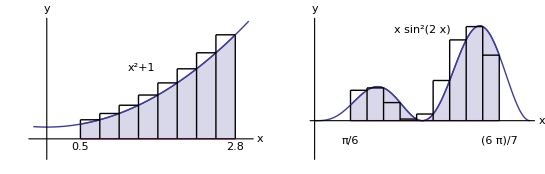

```mathematica
GraphicsRow[{
PlotRightEndpointApproximation[x^2+1,0.5,2.8,8,-0.2,3,-0.7,6,PlotRange->{-1.5,10},Ticks->False,AxesLabel->{x,y},{}],
PlotRightEndpointApproximation[x Sin[2x]^2,π/6,6/7 π,9,0,π,-0.5,2.3,PlotRange->{-0.9,2.5},Ticks->False,AxesLabel->{x,y},{}]
}]
```

Figure 3

The true area of the shaded region in Figure 1 is approximated by

∑_(i=1)^n f(a+i h) h or ∑_(i=0)^(n-1) f(a+(i+1) h) h.

```mathematica
RightEndpointApproximation[func_,a_,b_,n_]:=Module[
{f,h},
f[X_]=func/.x->X;
h=(b-a)/n//N;
Sum[f[a+i h],{i,1,n}]*h
];
```

```mathematica
RightEndpointApproximation[Sin[x],0,Pi,10]
```

1.98352

The animation below helps you explore the approximations using various number of subintervals for sin x over [0,π]. The exact area of the shaded region is 2.

```mathematica
Manipulate[
Module[{f,a,b,toString,PlotRightEndpointApproximation,RightEndpointApproximation},
f[x_]:=Sin[x];
a=0;b=π;
toString[x_]:=ToString[If[Abs[x]<10^-5,0,x]];

PlotRightEndpointApproximation[func_,a_,b_,n_,xMin_,xMax_,abYPos_,fYPos_,plotRange_,ticks_, axesLabel_, showExtraMsg_]:=Module[
{f,h=(b-a)/n},
f[X_]=func/.x->X;
Show[{ 
Plot[f[x],{x,xMin,xMax},plotRange,ticks,axesLabel,ImageSize->320],
Plot[{f[x],0},{x,a,b},Filling->{1->{2}}],
Graphics[{Text[a,{a,abYPos}]}],
Graphics[{Text[b,{b,abYPos}]}],
Graphics[{Text[f[x],{(xMin+xMax)/2,fYPos}]}],
{showExtraMsg},
Table[Graphics[Line[{{a+i*h,0},{a+i*h,Max[{f[a+i h],f[a+(i+1)*h]}]}}]],{i,0,n-1}],
Graphics[Line[{{b,0},{b,f[b]}}]],
Table[Graphics[Line[{{a+(i-1)*h,f[a+i*h]},{a+i*h,f[a+i*h]}}]],{i,1,n}]
}]
];
RightEndpointApproximation[func_,a_,b_,n_]:=Module[
{f,h},
f[X_]=func/.x->X;
h=(b-a)/n//N;
Sum[f[a+i h],{i,1,n}]*h
];

PlotRightEndpointApproximation[f[x],a,b,n,a-0.1,b+0.1,-0.1,1.2,PlotRange->{-0.3,1.3},Ticks->False,AxesLabel->{x,y},Graphics[{Text[StringJoin["n = ",ToString[n],"       Area ≈ ",toString[RightEndpointApproximation[f[x],a,b,n]]],{(a+b)/2,-0.2}]}]]],
{{n,10},1,200,1}]
```

(3) The midpoint approximation uses the value of f(x) at the midpoint of a subinterval as the height of the rectangle on the subinterval, as shown in figure 4.

```mathematica
(* For usage, see PlotLeftEndpointApproximation *)
PlotMidpointApproximation[func_,a_,b_,n_,xMin_,xMax_,abYPos_,fYPos_,plotRange_,ticks_, axesLabel_,showExtraMsg_]:=Module[
{f,h=(b-a)/n},
f[X_]=func/.x->X;
Show[{
Plot[f[x],{x,xMin,xMax},plotRange,ticks,axesLabel,ImageSize->250],
Plot[{f[x],0},{x,a,b},Filling->{1->{2}}],
Graphics[{Text[a,{a,abYPos}]}],
Graphics[{Text[b,{b,abYPos}]}],
Graphics[{Text[f[x],{(xMin+xMax)/2,fYPos}]}],
{showExtraMsg},
Table[Graphics[Line[{{a+i*h,0},{a+i*h,Max[{f[a+(i+0.5)*h],f[a+(i-0.5)*h]}]}}]],{i,0,n-1}],
Graphics[Line[{{b,0},{b,f[b-0.5h]}}]],
Table[Graphics[Line[{{a+(i-1)*h,f[a+(i-0.5)*h]},{a+i*h,f[a+(i-0.5)*h]}}]],{i,1,n}]
}]
];
```

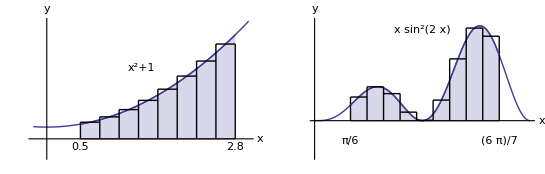

```mathematica
GraphicsRow[{
PlotMidpointApproximation[x^2+1,0.5,2.8,8,-0.2,3,-0.7,6,PlotRange->{-1.5,10},Ticks->False,AxesLabel->{x,y},{}],
PlotMidpointApproximation[x Sin[2x]^2,π/6,6/7 π,9,0,π,-0.5,2.3,PlotRange->{-0.9,2.5},Ticks->False,AxesLabel->{x,y},{}]
}]
```

Figure 4

The true area of the shaded region in Figure 1 is approximated by

∑_(i=1)^n f(a+(i-1/2) h) h or ∑_(i=0)^(n-1) f(a+(i+1/2) h) h.

```mathematica
MidpointApproximation[func_,a_,b_,n_]:=Module[
{f,h},
f[X_]=func/.x->X;
h=(b-a)/n//N;
Sum[f[a+(i-1/2) h],{i,1,n}]*h
];
```

```mathematica
MidpointApproximation[Sin[x],0,Pi,10]
```

2.00825

The animation below helps you explore the approximations using various number of subintervals for sin x over [0,π]. The exact area of the shaded region is 2.

```mathematica
Manipulate[
Module[{f,a,b,toString,PlotMidpointApproximation,MidpointApproximation},
f[x_]:=Sin[x];
a=0;b=π;
toString[x_]:=ToString[If[Abs[x]<10^-5,0,x]];

PlotMidpointApproximation[func_,a_,b_,n_,xMin_,xMax_,abYPos_,fYPos_,plotRange_,ticks_, axesLabel_,showExtraMsg_]:=Module[
{f,h=(b-a)/n},
f[X_]=func/.x->X;
Show[{
Plot[f[x],{x,xMin,xMax},plotRange,ticks,axesLabel,ImageSize->320],
Plot[{f[x],0},{x,a,b},Filling->{1->{2}}],
Graphics[{Text[a,{a,abYPos}]}],
Graphics[{Text[b,{b,abYPos}]}],
Graphics[{Text[f[x],{(xMin+xMax)/2,fYPos}]}],
{showExtraMsg},
Table[Graphics[Line[{{a+i*h,0},{a+i*h,Max[{f[a+(i+0.5)*h],f[a+(i-0.5)*h]}]}}]],{i,0,n-1}],
Graphics[Line[{{b,0},{b,f[b-0.5h]}}]],
Table[Graphics[Line[{{a+(i-1)*h,f[a+(i-0.5)*h]},{a+i*h,f[a+(i-0.5)*h]}}]],{i,1,n}]
}]
];
MidpointApproximation[func_,a_,b_,n_]:=Module[
{f,h},
f[X_]=func/.x->X;
h=(b-a)/n//N;
Sum[f[a+(i-1/2) h],{i,1,n}]*h
];

PlotMidpointApproximation[f[x],a,b,n,a-0.1,b+0.1,-0.1,1.2,PlotRange->{-0.3,1.3},Ticks->False,AxesLabel->{x,y},Graphics[{Text[StringJoin["n = ",ToString[n],"       Area ≈ ",toString[MidpointApproximation[f[x],a,b,n]]],{(a+b)/2,-0.2}]}]]],
{{n,10},1,200,1}]
```

(4) The trapezoidal approximation uses the values of f(x) at both endpoints and, thus, uses n trapezoids to represent the shaded region in figure 1, as shown in figure 5.

```mathematica
(* For usage, see PlotLeftEndpointApproximation *)
PlotTrapezoidalApproximation[func_,a_,b_,n_,xMin_,xMax_,abYPos_,fYPos_,plotRange_,ticks_, axesLabel_,showExtraMsg_]:=Module[
{f,h=(b-a)/n},
f[X_]=func/.x->X;
Show[{
Plot[f[x],{x,xMin,xMax},plotRange,ticks,axesLabel,ImageSize->250],
Plot[{f[x],0},{x,a,b},Filling->{1->{2}}],
Graphics[{Text[a,{a,abYPos}]}],
Graphics[{Text[b,{b,abYPos}]}],
Graphics[{Text[f[x],{(xMin+xMax)/2,fYPos}]}],
{showExtraMsg},
Table[Graphics[Line[{{a+i*h,0},{a+i*h,f[a+i*h]}}]],{i,0,n}],
Table[Graphics[Line[{{a+(i-1)*h,f[a+(i-1)*h]},{a+i*h,f[a+i*h]}}]],{i,1,n}]
}]
];
```

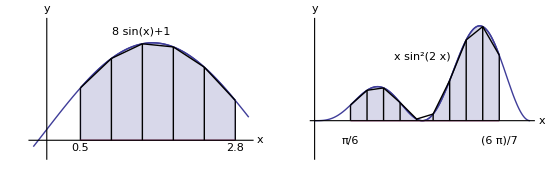

```mathematica
GraphicsRow[{
PlotTrapezoidalApproximation[8Sin[x]+1,0.5,2.8,5,-0.2,3,-0.7,10,PlotRange->{-1.5,11},Ticks->False,AxesLabel->{x,y},{}],
PlotTrapezoidalApproximation[x Sin[2x]^2,π/6,6/7 π,9,0,π,-0.5,1.6,PlotRange->{-0.9,2.5},Ticks->False,AxesLabel->{x,y},{}]
}]
```

Figure 5

The true area of the shaded region in Figure 1 is approximated by

∑_(i=1)^n (f(a+(i-1) h)+f(a+i h))/2 h or ∑_(i=0)^(n-1) (f(a+i h)+f(a+(i+1)h))/2 h.

```mathematica
TrapezoidalApproximation[func_,a_,b_,n_]:=Module[
{f,h},
f[X_]=func/.x->X;
h=(b-a)/n//N;
Sum[f[a+(i-1) h]+f[a+i h],{i,1,n}]*h/2
];
```

```mathematica
TrapezoidalApproximation[Sin[x],0,Pi,10]
```

1.98352

The animation below helps you explore the approximations using various number of subintervals for sin x over [0,π]. The exact area of the shaded region is 2.

```mathematica
Manipulate[
Module[{f,a,b,toString,PlotTrapezoidalApproximation,TrapezoidalApproximation},
f[x_]:=Sin[x];
a=0;b=π;
toString[x_]:=ToString[If[Abs[x]<10^-5,0,x]];

PlotTrapezoidalApproximation[func_,a_,b_,n_,xMin_,xMax_,abYPos_,fYPos_,plotRange_,ticks_, axesLabel_,showExtraMsg_]:=Module[
{f,h=(b-a)/n},
f[X_]=func/.x->X;
Show[{
Plot[f[x],{x,xMin,xMax},plotRange,ticks,axesLabel,ImageSize->320],
Plot[{f[x],0},{x,a,b},Filling->{1->{2}}],
Graphics[{Text[a,{a,abYPos}]}],
Graphics[{Text[b,{b,abYPos}]}],
Graphics[{Text[f[x],{(xMin+xMax)/2,fYPos}]}],
{showExtraMsg},
Table[Graphics[Line[{{a+i*h,0},{a+i*h,f[a+i*h]}}]],{i,0,n}],
Table[Graphics[Line[{{a+(i-1)*h,f[a+(i-1)*h]},{a+i*h,f[a+i*h]}}]],{i,1,n}]
}]
];
TrapezoidalApproximation[func_,a_,b_,n_]:=Module[
{f,h},
f[X_]=func/.x->X;
h=(b-a)/n//N;
Sum[f[a+(i-1) h]+f[a+i h],{i,1,n}]*h/2
];

PlotTrapezoidalApproximation[f[x],a,b,n,a-0.1,b+0.1,-0.1,1.2,PlotRange->{-0.3,1.3},Ticks->False,AxesLabel->{x,y},Graphics[{Text[StringJoin["n = ",ToString[n],"       Area ≈ ",toString[TrapezoidalApproximation[f[x],a,b,n]]],{(a+b)/2,-0.2}]}]]],
{{n,6},1,200,1}]
```

Example 1
Construct a table that shows the four basic numerical approximations for the area bounded by x=0,x=1,y=ⅇ^x, and y=0, corresponding to n=2,4,8,16,32,64.

```mathematica
Module[{f,a,b,h},
f[x_]:=ⅇ^x;
a=0;b=1;
h:=N[(b-a)/n]; (* delayed assignment is amazing ! *)
Join[
{{"n","Left-Endpoint", "Right-Endpoint","Midpoint","Trapezoidal"}},
Table[{
n,
Sum[f[a+i h],{i,0,n-1}]*h,
Sum[f[a+i h],{i,1,n}]*h,
Sum[f[a+(i-1/2) h],{i,1,n}]*h,
Sum[f[a+(i-1) h]+f[a+i h],{i,1,n}]*h/2
},{n,{2,4,8,16,32,64}}] (* or {n, 2^Range[6]} *)
]//TableForm
]
```

n | Left-Endpoint | Right-Endpoint | Midpoint | Trapezoidal
2 | 1.32436 | 2.1835 | 1.70051 | 1.75393
4 | 1.51244 | 1.94201 | 1.71382 | 1.72722
8 | 1.61313 | 1.82791 | 1.71716 | 1.72052
16 | 1.66514 | 1.77254 | 1.718 | 1.71884
32 | 1.69157 | 1.74527 | 1.71821 | 1.71842
64 | 1.70489 | 1.73174 | 1.71826 | 1.71832

Note: The exact value is ∫_0^1 ⅇ^x ⅆx=ⅇ-1≈1.71828.

Summary

We estimate the area under a continuous function f(x)≥0 for a≤x≤b, using n evenly-sized subintervals with h=△x=(b-a)/n.

(1) The left-endpoint approximation: ∑_(i=0)^(n-1) f(a+i h) h

(2) The right-endpoint approximation: ∑_(i=1)^n f(a+i h)

(3) The midpoint approximation: ∑_(i=1)^n f(a+(i-1)/2 h) h

(4) The trapezoidal approximation: ∑_(i=1)^n (f(a+(i-1) h)+f(a+i h))/2 h

## Riemann sum and definite integral

We are to test the four approximations at the same time with the same group of parameters. So, we first define the function

```mathematica
FourApproximations[func_,a_,b_,n_]:=Module[{f,h=N[(b-a)/n,9]},
f[X_]=func/.x->X;
{n,
Sum[f[a+i h],{i,0,n-1}]*h,
Sum[f[a+i h],{i,1,n}]*h,
Sum[f[a+(i-1/2) h],{i,1,n}]*h,
Sum[f[a+(i-1) h]+f[a+i h],{i,1,n}]*h/2
}
]
```

Now, we try to explore the results of approximating the area under y=x^2 over [0,1].

```mathematica
Module[{f,a=0,b=1},
f[x_]:=x^2;
Join[
{{"n","Left-Endpoint", "Right-Endpoint","Midpoint","Trapezoidal"}},
Table[FourApproximations[f[x],a,b,n],{n,{5,10,20,50,100,200,500,1000,10000}}] 
]//TableForm
]
```

n | Left-Endpoint | Right-Endpoint | Midpoint | Trapezoidal
5 | 0.24 | 0.44 | 0.33 | 0.34
10 | 0.285 | 0.385 | 0.3325 | 0.335
20 | 0.30875 | 0.35875 | 0.333125 | 0.33375
50 | 0.3234 | 0.3434 | 0.3333 | 0.3334
100 | 0.32835 | 0.33835 | 0.333325 | 0.33335
200 | 0.3308375 | 0.3358375 | 0.33333125 | 0.3333375
500 | 0.332334 | 0.334334 | 0.333333 | 0.333334
1000 | 0.3328335 | 0.3338335 | 0.33333325 | 0.3333335
10000 | 0.33328333 | 0.33338333 | 0.33333333 | 0.33333333

The midpoint and trapezoidal methods show better performance with different values of n, which can be proved in courses like numerical analysis (MATH 352). But when n is sufficient large, all four methods get closer to the exact value 1/3.

How about if we do not use a particular value of n ?

```mathematica
FourApproximations[x^2,0,1,n]//Rest
```

{((-1+n) (-1+2 n))/(6 n^2),((1+n) (1+2 n))/(6 n^2),(-1+4 n^2)/(12 n^2),(1+2 n^2)/(6 n^2)}

Each method returns a closed form expression! When a concrete value of n is given, how large the value of n is does not matter, and each just needs a small number of calculations.

Finally, let us find the limiting values of each method as n goes to infinity.

```mathematica
Limit[FourApproximations[x^2,0,1,n],n->∞]//Rest
```

{1/3,1/3,1/3,1/3}

Yes, they are all the same! This is consistent with the definition of the definite integral

∫_a^b f(x)ⅆx=limit_(n→∞)∑_(i=1)^n f(x_i^*)Δ x_i

if the limit of the Riemann sum ∑_(i=1)^n f(x_i^*)Δ x_i exists and keeps the same for arbitrarily chosen sample points x_i^*∈[x_(i-1),x_i],i=1,2,3,⋯,n, where {x_(0,)x_1,⋯,x_n} is an arbitrary partition of [a,b] with x_0=a,x_n=b, and max_(1≤i≤n) (|x_i-x_(i-1)|)  sufficiently small, provided f(x) is continuous on [a,b].

In reality, in our case, {x_0=0,x_1=h,x_2=2h,⋯,x_n=1} is one partition of [0,1] with h=Δ x_i=1/n. For the left-endpoint method, x_i^*=x_(i-1); for the right-endpoint method, x_i^*=x_i; for the midpoint method, x_i^*=(x_(i-1)+x_i)/2; and for the trapezoidal method, the intermediate-value theorem guarantees that we can choose x_i^*∈[x_(i-1),x_i] such that f(x_i^*)=(f(x_(i-1))+f(x_i))/2. In addition, every polynomial function is integrable, which means the limit of the Riemann sum exists. Therefore, the limiting values of all the four approximations must be the same in our example.

If f(x)≥0 for a≤x≤b, ∫_a^b f(x)ⅆx gives the exact area under the curve of f(x) and above the x-axis over [a,b]; otherwise, it specifies the net area. If the net area is zero, the areas above and under the x-axis are equal; if it is positive, more area is above the x-axis than under; otherwise, more area is under the x-axis than above.

## Finding exact area using Riemann sum

The code of the function PlotShadeInterval can be found in last section.

Example 2
Using the midpoint approximation, compute the exact area under the curve of f(x)=sin x over [0,π]. Plot the graph.

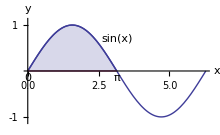

2.

```mathematica
f[x_]:=Sin[x];
a=0;b=Pi;
h=N[(b-a)/n];
PlotShadeInterval[f[x],a,b,0,2Pi,-0.15,0.7,PlotRange->{-1.1,1.1},Ticks->{{},{-1,1}},AxesLabel->{x,y}]
Limit[Sum[f[a+(i-1/2) h],{i,1,n}]*h,n->∞]
```

Example 3
Using the right-endpoint approximation, compute the exact area under the curve of f(x)=x sin x over [0,π]. Plot the graph.

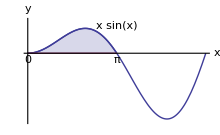

π

```mathematica
f[x_]:=x Sin[x];
a=0;b=Pi;
h=(b-a)/n;
PlotShadeInterval[f[x],a,b,0,2Pi,-0.5,2,PlotRange->{-5,2.4},Ticks->None,AxesLabel->{x,y}]
Limit[Sum[f[a+i h],{i,1,n}]*h,n->∞]
```

## Fundamental theorem of calculus

Assume that f(x) is continuous on [a,b]. By the fundamental theorem of calculus, if F(x) is an antiderivative of f(x), i.e., F'(x)=f(x), on [a,b], then

∫_a^b f(x)ⅆx=F(b)-F(a).

Therefore, there are two ways to evaluate ∫_a^b f(x)ⅆx. We can follow the definition of definite integral and find the limit of the Riemann sum ∑_(i=1)^n f(x_i^*)Δ x_i. We can also find first F(x), the antiderivative of f(x), and then evaluate F(b)-F(a). We usually take the second approach which allows us to apply known integral formulas as well as integration techniques. But knowing the original definition involving Riemann sum is the key to understand many other concepts, such as multiple integral, line integral, surface integral, and the derivation of many formulas, including the one for finding the arc length of parametric equations.

As discussed in Unit 8, the antiderivative of f(x) can be found by using ∫f(x)ⅆx or Integrate[f[x],x].

In reality, we can compute ∫_a^b f(x)ⅆx by using Mathematica built-in function Integrate[f[x],{x,a,b}] or ∫_a^b f[x]ⅆx.

Example 4
Applying the fundamental theorem of calculus, compute the exact area under the curve of f(x)=x sin x over [0,π].

First, find the antiderivative of f(x).

```mathematica
f[x_]:=x Sin[x]
F[x_]=Integrate[f[x],x]
```

-x Cos[x]+Sin[x]

Now, evaluate F(b)-F(a).

```mathematica
F[Pi]-F[0]
```

π

Example 5
Compute the exact area under the curve of f(x)=x sin x over [0,π].

```mathematica
∫_0^Pi x Sin[x]ⅆx
```

π

## Evaluating improper integrals

An improper integral is a definite integral ∫_a^b f(x)ⅆx of which at least one of the limits a and b is infinite or the integrand f(x) approaches infinity at one or more points on [a,b]. Since ∫_a^b f(x)ⅆx can be rewritten as ∫_c_1^c_2 f(x)ⅆx+∫_c_2^c_3 f(x)ⅆx+⋯+∫_(c_(n-1))^c_n f(x)ⅆx, where a=c_1<c_2<⋯<c_n=b , we can choose c_i,i=2,3,⋯,n-1, such that there is only one point, c_i or c_(i+1), on [c_i,c_(i+1)], at which f(x) goes to infinity. Therefore, there are basically two types of improper integrals.

Type I: At least one limit is infinity. For example, ∫_0^∞ xⅆx, ∫_(-∞)^1 xⅆx, and ∫_(-∞)^∞ xⅆx.

Type II: The integrand approaches infinity at one limit. E.g, ∫_0^1 1/x ⅆx and ∫_-2^1 1/(x-1)ⅆx.

The two types of improper integrals are defined below, given that a and b are constant.

∫_a^∞ f(x)ⅆx=limit_(t→∞)∫_a^t f(x)ⅆx, provided f(x) is continuous on [a,∞).
∫_(-∞)^b f(x)ⅆx=limit_(t→-∞)∫_t^b f(x)ⅆx, provided f(x) is continuous on (-∞,b].
∫_(-∞)^∞ f(x)ⅆx=limit_(t→-∞)∫_t^0 f(x)ⅆx+limit_(t→∞)∫_0^t f(x)ⅆx, provided f(x) is continuous on (-∞,∞).
∫_a^b f(x)ⅆx=limit_(t→a^+)∫_t^b f(x)ⅆx, provided f(x) is continuous on (a,b] and limit_(x→a^+)f(x)=∞.
∫_a^b f(x)ⅆx=limit_(t→b^-)∫_a^t f(x)ⅆx, provided f(x) is continuous on [a,b) and limit_(x→b^-)f(x)=∞.

An improper integral is said to be convergent if its defining limit exists; otherwise, it is said to be divergent.

For ∫_a^b f(x)ⅆx=∫_c_1^c_2 f(x)ⅆx+∫_c_2^c_3 f(x)ⅆx+⋯+∫_(c_(n-1))^c_n f(x)ⅆx, if any one of the improper integrals on the right hand side is divergent, ∫_a^b f(x)ⅆx is divergent.

Example 6
Evaluate ∫_1^∞ x^-3 ⅆx.

```mathematica
Assuming[t>1,Integrate[x^-3,{x,1,t}]]
Limit[%,t->∞]
```

1/2-1/(2 t^2)

1/2

So, the improper integral is convergent.

Example 7
Evaluate ∫_(-∞)^∞ 1/(√(1+x^2))ⅆx.
Rewrite ∫_(-∞)^∞ 1/(√(1+x^2))ⅆx=∫_(-∞)^0 1/(√(1+x^2))ⅆx+∫_0^∞ 1/(√(1+x^2))ⅆx.
Now, evaluate the first improper integral on the right hand side.

```mathematica
Assuming[t<0,Integrate[1/(√(1+x^2)),{x,t,0}]]
Limit[%,t->-∞]
```

-ArcSinh[t]

∞

Thus, ∫_(-∞)^∞ 1/(√(1+x^2))ⅆx is divergent, which means the area between the curve of the integrand, which is nonnegative, and the x-axis is unbounded.

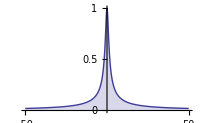

```mathematica
Plot[1/(√(1+x^2)),{x,-50,50},PlotRange->All,Filling->Axis,Ticks->{{-50,50},{0,0.5,1}},ImageSize->200]
```

Example 8
Evaluate ∫_-1^1 1/x^2 ⅆx and determine its convergence.
Rewrite ∫_-1^1 1/x^2 ⅆx=∫_-1^0 1/x^2 ⅆx+∫_0^1 1/x^2 ⅆx because x=0 is the point where the integrand goes to infinity.
Now, evaluate first ∫_-1^0 1/x^2 ⅆx.

```mathematica
Assuming[-1<t<0,Integrate[1/x^2,{x,-1,t}]]
```

-(1+t)/t

```mathematica
Limit[%,t->0,Direction->1]
```

∞

Therefore, ∫_-1^1 1/x^2 ⅆx is divergent.

## Finding area for complicated cases

If f(x) is continuous and non-negative on [a,b], the definite integral ∫_a^b f(x)ⅆx gives exactly the area of the region bounded by x=a,x=b,y=0, and y=f(x).

Example 9
Find the area under f(x)=x sin x on [π/2,π].

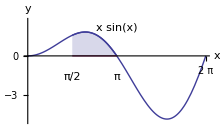

2.14159

```mathematica
f[x_]:=x Sin[x]
a=Pi/2;b=Pi;
PlotShadeInterval[f[x],a,b,0,2Pi,-1.6,2.2,PlotRange->{-5,2.7},Ticks->{{2π},{}},AxesLabel->{x,y}]
Integrate[f[x],{x,Pi/2,Pi}]//N
```

Example 10
Find the area enclosed by x=π,x=2π,y=0, and f(x)=x sin x.

From the graph in previous example, we know f(x)≤0 and, thus, we cannot compute ∫_π^(2π) x sin xⅆx for the area.

```mathematica
Integrate[x Sin[x],{x,π,2π}]
```

-3 π

which does not make sense.

But this does not mean we cannot find the area at all. If you reflect the curve of f(x) about the x-axis, we will obtain the curve of g(x)=-f(x). Moreover, if the curve of f(x) is below the x-axis, then the curve of g(x) is above the x-axis. Due to the symmetry of the two curves about the x-axis, we know the area between the x-axis and f(x) is the same as the area between g(x) and the x-axis, both from x=a to x=b.

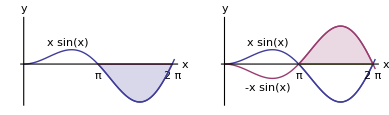

-Graphics-

Therefore, the area is given by

∫_a^b g(x)ⅆx=∫_a^b -f(x)ⅆx=-∫_a^b f(x)ⅆx.

Thus, the area to be found is

```mathematica
-Integrate[x Sin[x],{x,Pi,2Pi}]
```

3 π

Example 11
Plot the graph showing the region enclosed by x=2,x=3,f(x)=x sin x, and g(x)=x^2. Compute the area of that region.

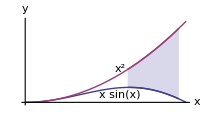

```mathematica
Module[{f,g,a=2,b=3,abYPos=-1.4,fYPos=2.8,xMin=0,xMax=Pi},
f[x_]:=x Sin[x];
g[x_]:=x^2;
Show[{
Plot[{f[x],g[x]},{x,0,Pi},PlotRange->{-0.1,10},Ticks->None,AxesLabel->{x,y},PlotStyle->Automatic,ImageSize->200],
Plot[{f[x],g[x]},{x,a,b},Filling->{1->{2}}],
Graphics[{Text[a,{a,abYPos}]}],
Graphics[{Text[b,{b,abYPos}]}],
Graphics[{Text[f[x],{(xMin+xMax)/1.7,0.9}]}],
Graphics[{Text[g[x],{(xMin+xMax)/1.7,4}]}]
}]]
```

In this case, the area is given by ∫_a^b top(x)-bottom(x)ⅆx where top(x) is the function whose curve is on the top of the other’s one on [a,b], and bottom(x) is the other function. Therefore, according to the graph, the area is

```mathematica
Integrate[x^2-x Sin[x],{x,2,3}]//N
```

4.96383

Example 12
Plot the graph showing the region enclosed by x=1,x=3,f(x)=x sin x, and g(x)=1/4 x^2. Compute the area of that region.

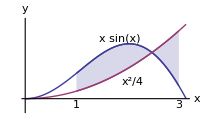

```mathematica
Module[{f,g,a=1,b=3,abYPos=-0.2,fYPos=1.8,xMin=0,xMax=Pi},
f[x_]:=x Sin[x];
g[x_]:=1/4x^2;
Show[{
Plot[{f[x],g[x]},{x,0,Pi},PlotRange->{-0.4,2.6},Ticks->None,AxesLabel->{x,y},PlotStyle->Automatic,ImageSize->200],
Plot[{f[x],g[x]},{x,a,b},Filling->{1->{2}}],
Graphics[{Text[a,{a,abYPos}]}],
Graphics[{Text[b,{b,abYPos}]}],
Graphics[{Text[f[x],{(xMin+xMax)/1.7,2.0}]}],
Graphics[{Text[g[x],{(xMin+xMax)/1.5,0.55}]}]
}]]
```

According to the graph, the intersection of the two curves occurs on (1,3). It divides the interval [1,3] into two subintervals [1,x_0] and [x_0,3]. The position of a curve relative to the other changes from one subinterval to the other. So, we need to find x_0 first by

```mathematica
NSolve[x Sin[x]==1/4 x^2&&1≤x≤3,x]
```

{{x→2.47458}}

```mathematica
x0=x/.%[[1]]
```

2.47458

Now, we can find the area between the two curves on [1,x_0] by ∫_1^x_0 (x sin x-1/4 x^2)ⅆx and the area on [x_0,3] by ∫_x_0^3 (1/4 x^2-x sin x)ⅆx, and then find their sum.

```mathematica
Integrate[x Sin[x]-1/4 x^2,{x,1,x0}]+Integrate[1/4 x^2-x Sin[x],{x,x0,3}]
```

1.52124

How about using ∫_a^b |f(x)-g(x)|ⅆx? Mathematically, it is absolutely correct.

```mathematica
Integrate[Abs[x Sin[x]-1/4 x^2],{x,1,3}]//N
```

1.52124

Yes, it works! However, we should not 100% depend on computers. I have seen many times the Mathematica function, Abs, works and then fails. Do you really like solving equations, integrating or differentiating functions, with variables inside the two vertical bars? I don’t believe so because it tends to make calculation much more complicated. If it is tough for us, it is often tough for computer, too. Computer is just a diligent and tireless tool of us if we can teach it how to work. The same reason, if we do not understand how to interpret a double or triple integral, a super computer will be no help.

Example 13
Find the area of the region enclosed by the two parabolas y=(x-1)^2-5 and y=(x+1)^2+5.

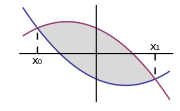

```mathematica
f[x_]:=(x-1)^2-5;
g[x_]:=-(x+1)^2+5;

Module[{xs},
xs=x/.NSolve[f[x]==g[x],x];
Show[{
Plot[{f[x],g[x]},{x,-2.5,2.5},Filling->{1->{2}},FillingStyle->{LightGray,White},Ticks->None,ImageSize->180],
Graphics[{Dashed,Line[{{xs[[1]],0},{xs[[1]],f[xs[[1]]]}}]}],
Graphics[{Dashed,Line[{{xs[[2]],0},{xs[[2]],f[xs[[2]]]}}]}],
Graphics[Text["x_0",{xs[[1]],-1.1}]],
Graphics[Text["x_1",{xs[[2]],1.1}]]
}]]
```

To find the area of the shaded region, we need to find x_0 and x_1 first.

```mathematica
xs=x/.NSolve[f[x]==g[x],x]
```

{-2.,2.}

```mathematica
x0=xs[[1]];x1=xs[[2]];
```

For any parabola y=(a(x-k))^2+h, if a>0, its curve is concave upward; if a<0, its curve is concave downward. Now, based on the graph, g(x) is on the top of f(x). Therefore, the area of the shaded region is

```mathematica
Integrate[g[x]-f[x],{x,x0,x1}]
```

21.3333

Example 14
Draw two circles, x^2+y^2=4 and (x-2)^2+y^2=1, with the enclosed region inside both shaded. Computer the area of the shaded region.

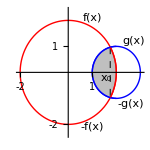

```mathematica
f[x_]:=Sqrt[4-x^2]
g[x_]:=Sqrt[1-(x-2)^2]
x0=x/.NSolve[f[x]==g[x],x][[1]];

Show[
Plot[{f[x],-f[x],g[x],-g[x]},{x,-2.05,3.05},AspectRatio->Automatic,PlotRange->{-2.4,2.4},PlotStyle->{Red,Red,Blue,Blue},Ticks->{{-2,-1,1,2},{-2,-1,1,2}},ImageSize->150],Plot[{f[x],-f[x],g[x],-g[x]},{x,x0,2},AspectRatio->Automatic,PlotStyle->{Red,Red,Blue,Blue},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Gray]],Plot[{g[x],-g[x]},{x,1,x0},AspectRatio->Automatic,PlotStyle->{Blue,Blue},Filling->{{1->{2}}},FillingStyle->Directive[Opacity[0.5],Gray]],
Graphics[{Dashed,Line[{{x0,f[x0]},{x0,-f[x0]}}]}],
Graphics[Text["x_0",{x0-0.15,-0.2}]],
Graphics[Text["f(x)",{1,2.1}]],
Graphics[Text["-f(x)",{1,-2.1}]],
Graphics[Text["g(x)",{2.7,1.2}]],
Graphics[Text["-g(x)",{2.6,-1.2}]]
]
```

In Cartesian coordinate system, we cannot use one function to describe a circle because it cannot pass the vertical line test. But we can use two functions, one for the upper semicircle, and one for the other half. For example, from the circle x^2+y^2=4, we obtain y=±√(4-x^2) which are actually two functions, i.e., f(x)=√(4-x^2)and f_1(x)=-√(4-x^2)=-f(x).

The shaded region consists of two parts separated by the dashed vertical line connecting the two intersections of the two circles. Let x_0 denote the x-coordinate of two intersections. The area of the shaded region is

```mathematica
Integrate[g[x]-(-g[x]),{x,1,x0}]+Integrate[f[x]-(-f[x]),{x,x0,2}]
```

1.40307

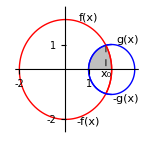

-Graphics-

Due to the symmetry of the shaded region about the x-axis, the area of the shaded region is twice of the area of the part above the x-axis. So, we can also compute it by the command

```mathematica
2(Integrate[g[x],{x,1,x0}]+Integrate[f[x],{x,x0,2}])
```

1.40307

Example 15
Find the area of the region bounded by two curves y=2x-2 and y^2=x.

The curve y^2=x is not for a function y=f(x). We can handle it like what we do with circles in the previous example, i.e., interpreting it as two functions, y=f(x)=√x and y=-√x=-f(x).

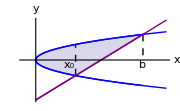

```mathematica
Module[{f,h,x0,b},
f[x_]:=√x;
g[x_]:=2x-2;
x0=x/.NSolve[-f[x]==g[x],x][[1]];
b=x/.NSolve[f[x]==g[x],x][[1]];
Show[{
Plot[{f[x],-f[x],g[x]},{x,-0.2,2},PlotRange->{-2,2},PlotStyle->{Blue,Blue,Purple},Ticks->None,AxesLabel->{x,y},ImageSize->180],
Plot[{f[x],-f[x],g[x]},{x,0,x0},PlotStyle->{Blue,Blue,Purple},Filling->{1->{2}}],
Plot[{f[x],-f[x],g[x]},{x,x0,b},PlotStyle->{Blue,Blue,Purple},Filling->{3->{1}}],
Graphics[{Dashed,Line[{{x0,-f[x0]},{x0,f[x0]}}]}],
Graphics[{Dashed,Line[{{b,g[b]},{b,0}}]}],
Graphics[Text["x_0",{x0-0.09,-0.25}]],
Graphics[Text["b",{b,-0.25}]]
}]]
```

```mathematica
f[x_]:=√x
g[x_]:=2x-2
x0=x/.NSolve[-f[x]==g[x],x][[1]];
b=x/.NSolve[f[x]==g[x],x][[1]];
```

```mathematica
Integrate[√x-(-√x),{x,0,x0}]+Integrate[√x-(2x-2),{x,x0,b}]
```

1.46027

In this case, we may also interpret x as a function of y, i.e., x=f(y)=1/2 x+1 and x=g(y)=y^2.

With y=f(x) and y=g(x), if the curve of f(x) is always above that of g(x) for a≤x≤b, then the area of the region bounded by x=a,x=b,y=f(x), and y=g(x) is given by ∫_a^b f(x)-g(x)ⅆx. Similarly, with x=f(y) and x=g(y), if the curve of f(y) is always on the right side of g(y) for a≤y≤b, then the area of the region bounded by x=f(y),x=g(y),y=a, and y=b is given by ∫_a^b f(y)-g(y)ⅆy.

We can use ContourPlot to draw the graph, and determine if one curve is on the right side of the other on the interval of interest.

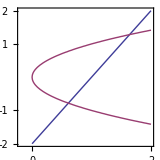

```mathematica
ContourPlot[{y==2x-2,y^2==x},{x,-0.2,2},{y,-2,2},FrameTicks->{{0,1,2},{-2,-1,1,2}},ImageSize->160]
```

Indeed, y=2x-2 (or x=1/2 y+1) is always on the right side of x=y^2 when the enclosed region is concerned. Now, we need to find the interval of y values.

```mathematica
ys=y/.NSolve[{y==2x-2,y^2==x},{x,y}]
```

{-0.780776,1.28078}

Thus, y changes from -0.780776 to 1.28078. Therefore, the area of the bounded region equals to

```mathematica
Integrate[1/2 y+1-y^2,{y,ys[[1]],ys[[2]]}]
```

1.46027

Example 16
Refer to the following graph. Determine the value of h such that the area of the two shaded regions are equal.

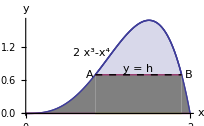

-Graphics-

```mathematica
Clear[h]
f[x_]:=2 x^3-x^4
```

Let x_a and x_b denote the x-coordinates of points A and B, respectively. Then we establish the equation

∫_0^x_a f(x)ⅆx+∫_x_a^x_b hⅆx+∫_x_b^2 f(x)ⅆx=∫_x_a^x_b [f(x)-h]ⅆx ⋯⋯⋯ (1)

Since points A and B are on the curve of f(x) and the line y=h as well, we have

f(x_a)=h ⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯ (2)
f(x_b)=h ⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯ (3)

Therefore, we have three equations (1), (2) and (3) in three variables h,x_a and x_b. Solving this system of equations,

```mathematica
NSolve[{f[xa]==h,f[xb]==h,∫_0^xa f[x]ⅆx+∫_xa^xb hⅆx+∫_xb^2 f[x]ⅆx==∫_xa^xb (f[x]-h)ⅆx},{xa,xb,h},Reals]
```

{{xa→0.774513,xb→1.91949,h→0.569371}}

we obtain the value of h

```mathematica
h/.%[[1]]
```

0.569371

## Simpson’s 1/3 and 3/8 methods

The four area approximations are really basic ones. They all uses a simple straight line to approximate the curve of f(x) on a subinterval [x_(i-1),x_i],i=1,2,⋯,n. For example, the left-endpoint method uses a horizontal straight line y=f(x_(i-1)), and the trapezoidal method uses a straight line y=f(x_i)+(f(x_i)-f(x_(i-1)))/h(x-x_i).

Simpson’s 1/3 and 3/8 methods use quadratic and cubic polynomials to approximate f(x) over two and three consecutive subintervals, respectively. We will not derive the formulas here for it takes time. You can find related discussion in numerical computing courses. In brief, for Simpson’s 1/3 method, the area under f(x) for x_i≤x≤x_(i+2) is given by

1/3 h [f(x_i)+4f(x_(i+1))+f(x_(i+2))] with n divisible by 2;

and for Simpson’s 3/8 method, the area is approximated by

3/8 h [f(x_i)+3f(x_(i+1))+3f(x_(i+2))+f(x_(i+3))] with n divisible by 3.

```mathematica
Simpson13Approximation[func_,a_,b_,n_]:=Module[{f,h=N[(b-a)/n,8]},
f[X_]=func/.x->X;
1/3 h Sum[f[a+i h]+4f[a+(i+1) h]+f[a+(i+2)h],{i,0,n-2,2}]]
```

```mathematica
Simpson38Approximation[func_,a_,b_,n_]:=Module[{f,h=N[(b-a)/n,8]},
f[X_]=func/.x->X;
3/8 h Sum[f[a+i h]+3f[a+(i+1) h]+3f[a+(i+2)h]+f[a+(i+3)h],{i,0,n-3,3}]]
```

```mathematica
{Simpson13Approximation[E^x,0,1,30],Simpson38Approximation[E^x,0,1,30]}
```

{1.718282,1.718282}

```mathematica
{Simpson13Approximation[E^x,0,1,n],Simpson38Approximation[E^x,0,1,n]}//Simplify
```

{((-1+ⅇ) (1+4 ⅇ^(1/n)+ⅇ^(2/n)))/(3 (-1+ⅇ^(2/n)) n),(3 (-1+ⅇ) (1+ⅇ^(1/n))^3)/(8 (-1+ⅇ^(3/n)) n)}

Each has a closed form formula again, and has the same limiting value as n→∞.

```mathematica
Limit[%,n->∞]
```

{-1+ⅇ,-1+ⅇ}

Note: The above code for Simpson13Approximation and Simpson38Approximation works. However, we notice that, for example, with Simpson’s 1/3 rule, when it is applied to [x_0,x_2], f(x_2) is calculated once; when it is applied to [x_2,x_4], f(x_2) is calculated the second time, or in general, f(x_i) are calculated twice for i=2,4,6,⋯,n-2. Better implementation should remove this kind of repetition.

Now, let us compare all six approximations together in a table.

Example 17
Construct a table that shows the four basic numerical approximations, left-endpoint, right-endpoint, midpoint, and trapezoidal approximations as well as Simpson’s 1/3 and 3/8 methods, for the area bounded by x=0,x=1,y=0, and y=x^2, corresponding to n=1,2,3,4, 5,6,12,24,48, 96,192,384,768, 1536,3072,6144,12288.

```mathematica
(* n must be divisible by both 2 and 3 *)
SixApproximations[func_,a_,b_,n_]:=Module[{f,h=(b-a)/n,d=7},
f[X_]=func/.x->X;
{n,
N[Sum[f[a+i h],{i,0,n-1}]*h,d],
N[Sum[f[a+i h],{i,1,n}]*h,d],
N[Sum[f[a+(i-1/2) h],{i,1,n}]*h,d],
N[Sum[f[a+(i-1) h]+f[a+i h],{i,1,n}]*h/2,d],
If[Mod[n,2]==0,(* divisible by 2 *)
N[1/3*h*Sum[f[a+i h]+4f[a+(i+1) h]+f[a+(i+2)h],{i,0,n-2,2}],d],
"N/A"],
If[Mod[n,3]==0,(* divisible by 3 *)
N[3/8*h*Sum[f[a+i h]+3f[a+(i+1) h]+3f[a+(i+2)h]+f[a+(i+3)h],{i,0,n-3,3}] ,d],
"N/A"]
}
]
```

```mathematica
Module[{f,a=0,b=1},
f[x_]:=x^2;
TableForm[
Join[
{{"n","Left-End", "Right-End","Midpoint","Trapezoid","Simpson 1/3", "Simpson 3/8"}},
Table[SixApproximations[f[x],a,b,n],{n,{1,2,3,4,5,6,12,24,48,96,192,384,768,1536,3072,6144,12288}}]
],TableAlignments->Right]
]
```

n | Left-End | Right-End | Midpoint | Trapezoid | Simpson 1/3 | Simpson 3/8
1 | 0 | 1. | 0.25 | 0.5 | N/A | N/A
2 | 0.125 | 0.625 | 0.3125 | 0.375 | 0.3333333 | N/A
3 | 0.1851852 | 0.5185185 | 0.3240741 | 0.3518519 | N/A | 0.3333333
4 | 0.21875 | 0.46875 | 0.328125 | 0.34375 | 0.3333333 | N/A
5 | 0.24 | 0.44 | 0.33 | 0.34 | N/A | N/A
6 | 0.2546296 | 0.4212963 | 0.3310185 | 0.337963 | 0.3333333 | 0.3333333
12 | 0.2928241 | 0.3761574 | 0.3327546 | 0.3344907 | 0.3333333 | 0.3333333
24 | 0.3127894 | 0.354456 | 0.3331887 | 0.3336227 | 0.3333333 | 0.3333333
48 | 0.322989 | 0.3438223 | 0.3332972 | 0.3334057 | 0.3333333 | 0.3333333
96 | 0.3281431 | 0.3385598 | 0.3333243 | 0.3333514 | 0.3333333 | 0.3333333
192 | 0.3307337 | 0.335942 | 0.3333311 | 0.3333379 | 0.3333333 | 0.3333333
384 | 0.3320324 | 0.3346365 | 0.3333328 | 0.3333345 | 0.3333333 | 0.3333333
768 | 0.3326826 | 0.3339847 | 0.3333332 | 0.3333336 | 0.3333333 | 0.3333333
1536 | 0.3330079 | 0.3336589 | 0.3333333 | 0.3333334 | 0.3333333 | 0.3333333
3072 | 0.3331706 | 0.3334961 | 0.3333333 | 0.3333334 | 0.3333333 | 0.3333333
6144 | 0.333252 | 0.3334147 | 0.3333333 | 0.3333333 | 0.3333333 | 0.3333333
12288 | 0.3332926 | 0.333374 | 0.3333333 | 0.3333333 | 0.3333333 | 0.3333333

Are you surprised at the huge difference in the performance of these methods? According to the table, the Simpson’s methods each get 0.3333333 just in one attempt. For the same goal, the midpoint and trapezoidal approximations need at least 769 and 3073 attempts, respectively. And for the left- and right-endpoint methods, 12,288 attempts cannot help. It seems that the Simpson’s methods take no time to obtain a precise solution. Indeed, they converge to the exact value 1/3 much faster than the four basic approximations. In numerical computing class, we will be able to give an analytical description of the difference.

The huge difference in the performance of various algorithms presents one strong reason why many science and engineering majors should take a numerical computing course. In the course, all the six approximation methods here are just a few of all discussed in chapters on numerical integration. Other typical topics covered in the course include finding roots of functions, curve fitting and interpolation, solving systems of equations, numerical differentiation, differential equations with initial or boundary conditions, etc.

© 2015-2023 by David Wang, dwang@liberty.edu